# QNM Poschl-Teller potential cut, three regions

# Grid points

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Prec=14 MachinePrecision;
a=N[4, Prec];
b=N[7, Prec];
b=b/10;
a=a/10;
Nz=40;
NzHigh=2 Nz;
z0=a;
z1=b;
Δz=z1-z0;
xf[i_,Nz_]:=Cos[(π i)/Nz];
xtot=N[Table[xf[i,Nz],{i,0,Nz}],Prec ];
xx=N[Table[z0+1/2 Δz (1+xf[i,Nz]),{i,0,Nz}],Prec ];
z0=-1;
z1=a;
Δz=z1-z0;
y1f[i_,Nz_]:=Cos[(2 π i)/(2 Nz +1)];
yy1=N[Table[z0+1/2 Δz (1+y1f[i,Nz]),{i,0,Nz}],Prec ];
z0=b;
z1=1;
Δz=z1-z0;
y2f[i_,Nz_]:=- Cos[(2 π i)/(2 Nz +1)];
yy2=N[Table[z0+1/2 Δz (1+y2f[i,Nz]),{i,0,Nz}],Prec ];
```

# Lobatto differential matrices

```mathematica
Id=IdentityMatrix[Nz+1];
Zero=ConstantArray[0,{Nz+1,Nz+1}];
k[i_,Nz_]:=If[i*(i-Nz)==0, 2,1];
dx1[i_,j_,Nz_]:=If[i≠j,
N[(k[i,Nz]/k[j,Nz])*(-1)^(i-j)/(xf[i, Nz]-xf[j, Nz]), Prec], 0
];
 D1 =N[Table[dx1[i,j,Nz], {i,0,Nz}, {j,0,Nz}] ,Prec  ];

For[i=2, i≤Nz, i++,
D1[[i,i]]= N[-xf[i-1, Nz]/(2*(1-xf[i-1, Nz]^2)),Prec  ];
];
D1[[1,1]]=N[(2 *(Nz)^2+1)/6 , Prec ];
D1[[Nz +1, Nz +1]]=N[-(2 *(Nz)^2+1)/6 , Prec];

dx2[i_,j_,Nz_]:=If[i≠j && i ≠ 0 && i ≠ Nz,
N[(((-1)^(i-j))/k[j,Nz])*((xf[i, Nz])^2+xf[i, Nz]*xf[j, Nz]-2)/((1-(xf[i, Nz])^2)*(xf[j, Nz] - xf[i, Nz])^2), Prec]
,0
];
dx20[j_,Nz_]:= If[j ≠ 0,
N[((2/3)*(-1)^(j)/k[j, Nz])*((2*(Nz)^2+1)*(1-xf[j, Nz])-6)/(1-xf[j, Nz])^2 ,Prec ]
, Unevaluated[Sequence[]]
];
dx2N[j_,Nz_]:= If[j ≠Nz,
 N[((2/3)*(-1)^(Nz + j)/k[j, Nz])*((2*(Nz)^2+1)*(1+xf[j, Nz])-6)/(1+xf[j, Nz])^2 ,Prec ]
, Unevaluated[Sequence[]]
];
D2 =N[Table[dx2[i,j,Nz], {i,0,Nz }, {j,0,Nz}] ,Prec  ];
For[j=2, j≤Nz+1, j++,
D2[[1,j]]= dx20[j-1, Nz];
];
For[j=1, j≤Nz, j++,
D2[[Nz +1,j]]= dx2N[j-1, Nz];
];

For[i=2, i≤Nz, i++,
D2[[i,i]]= N[(-1/(1-(xf[i-1, Nz])^2)^2) -(Nz^2 -1)/(3*(1-xf[i-1, Nz]^2)),Prec  ];
];
D2[[1,1]]=N[((Nz)^4-1)/15 ,Prec ];
D2[[Nz +1, Nz +1]]= N[((Nz)^4-1)/15, Prec  ];
```

# Left & Right Radau differentiation matrices

```mathematica
dy1[i_,j_,Nz_]:=If[i≠j && i ≠ 0 && j ≠ 0,
N[(((-1)^(i-j))/(y1f[i, Nz]-y1f[j, Nz]))*N[Sqrt[(1+y1f[j, Nz])/(1+y1f[i, Nz])] ,Prec  ] ,Prec ],0
];
 dy10[j_,Nz_]:= If[j ≠ 0,
N[  (((-1)^(j))*Sqrt[2*(y1f[j,Nz]+1)]/(-y1f[j, Nz]+1)) ,Prec ]
, Unevaluated[Sequence[]]
];
dy1N[i_,Nz_]:= If[i≠0,
N[ ((-1)^(i+1))/(Sqrt[2]*Sqrt[ y1f[i, Nz]+1]*(-y1f[i, Nz]+1))  ,Prec ]
, Unevaluated[Sequence[]]
];
 Dy11 =N[Table[dy1[i,j,Nz], {i,0,Nz }, {j,0,Nz}] ,Prec  ];
For[j=2, j≤Nz+1, j++,
Dy11[[1,j]]= dy10[j-1, Nz];
];
For[i=2, i≤Nz +1, i++,
Dy11[[i,1]]= dy1N[i-1, Nz];
];

For[i=2, i≤Nz+1, i++,
Dy11[[i,i]]= N[-1/(2*(1-y1f[i-1, Nz]^2)),Prec  ];
];
Dy11[[1,1]]=N[Nz*(Nz +1)/3 ,Prec ];
dy12[i_,j_,Nz_]:=If[i≠j && i ≠ 0 && j ≠ 0,
N[((-1)^(i-j))*(2*(y1f[i, Nz])^2-y1f[i, Nz]+y1f[j, Nz]-2)/(((y1f[i, Nz]-y1f[j, Nz])^2)*(1-(y1f[i, Nz])^2))*Sqrt[(1+y1f[j, Nz])/(1+y1f[i, Nz])] ,Prec  ] ,0

];
 dy120[j_,Nz_]:= If[j ≠ 0,
N[  ((((-1)^(j))*2*Sqrt[2] *Sqrt[1+ y1f[j, Nz]])/(3*(-y1f[j, Nz]+1)^2))* (Nz *(Nz +1)*(1 - y1f[j, Nz])-3) ,Prec ]
, Unevaluated[Sequence[]]
];
dy12N[i_,Nz_]:= If[i≠0,
N[ ((-1)^(i+1))*(2*y1f[i, Nz] +1)/(Sqrt[2]*( y1f[i, Nz]+1)^(3/2)*(-y1f[i, Nz]+1)^2) ,Prec  ]
, Unevaluated[Sequence[]]
];
 Dy12 =N[Table[dy12[i,j,Nz], {i,0,Nz }, {j,0,Nz}] ,Prec  ];
For[j=2, j≤Nz+1, j++,
Dy12[[1,j]]= dy120[j-1, Nz];
];
For[i=2, i≤Nz +1, i++,
Dy12[[i,1]]= dy12N[i-1, Nz];
];

For[i=2, i≤Nz+1, i++,
Dy12[[i,i]]= N[(-Nz*(Nz +1)/(3*(1-(y1f[i-1, Nz])^2))) - (y1f[i-1, Nz]/(1-y1f[i-1, Nz]^2)^2) ,Prec ];
];

Dy12[[1,1]]=N[(Nz -1)*Nz*(Nz +1)*(Nz+2)/15 ,Prec ];
```

# Adapted matrices to three regions

```mathematica
Dy21=-Dy11;
Dy22 = Dy12;
Dy221=N[(2/(1-b))*Dy21 ,Prec ];
Dy222=N[((2/(1-b))^2)*Dy22 ,Prec ];

yy1=Reverse[yy1];
xx=Reverse[xx];

Dy111=N[(2/(a+1))*Dy11 ,Prec  ];
Dy112=N[((2/(a+1))^2)*Dy12 ,Prec ];
Dx1=N[(2/(b-a))*D1 ,Prec ];
Dx2=N[((2/(b-a))^2)*D2 ,Prec ];
Dy111=Reverse[Reverse[Dy111,2],1];
Dy112=Reverse[Reverse[Dy112,2],1];
Dx1=Reverse[Reverse[Dx1,2],1];
Dx2=Reverse[Reverse[Dx2,2],1];
```

```mathematica
s1=N[(1+yy1)/2,Prec ];
sx=N[(1+xx)/2,Prec ];
s2=N[(1+yy2)/2,Prec ];
Ds11=N[2*Dy111,Prec ];
Ds12=N[4*Dy112,Prec ];
Dsx1=N[2*Dx1,Prec ];
Dsx2=N[4*Dx2,Prec ];
Ds21=N[2*Dy221,Prec ];
Ds22=N[4*Dy222,Prec ];
```

# Eigenvalue problem matrices

```mathematica
LL1s1=(1/(1+s1))*(2*s1*(1-s1)*Ds11 -(s1^2)*Ds11 + (s1^2)*(1-s1)*Ds12 -(6-3*s1)*Id);
LL1sx=(1/(1+sx))*(2*sx*(1-sx)*Dsx1 -(sx^2)*Dsx1 + (sx^2)*(1-sx)*Dsx2 -(6-3*sx)*Id);
LL1s2=(1/(1+s2))*(2*s2*(1-s2)*Ds21 -(s2^2)*Ds21 + (s2^2)*(1-s2)*Ds22 -(6-3*s2)*Id);


L1s1=(1/(1+s1))*(2*s1*(1-s1)*Ds11 -(s1^2)*Ds11 + (s1^2)*(1-s1)*Ds12 );
L1sx=(1/(1+sx))*(2*sx*(1-sx)*Dsx1 -(sx^2)*Dsx1 + (sx^2)*(1-sx)*Dsx2 -(6-3*sx)*Id);
L1s2=(1/(1+s2))*(2*s2*(1-s2)*Ds21 -(s2^2)*Ds21 + (s2^2)*(1-s2)*Ds22);

L2s1=(1/(1+s1))*((1-2*s1^2)*Ds11 -2*s1*Id);
L2sx=(1/(1+sx))*((1-2*sx^2)*Dsx1 -2*sx*Id);
L2s2=(1/(1+s2))*((1-2*s2^2)*Ds21 -2*s2*Id);


Msx=ArrayFlatten[{
{Zero,Id} , 
{L1sx,L2sx} }];

Ms1=ArrayFlatten[{
{Zero,Id} , 
{L1s1,L2s1} }];

Ms2=ArrayFlatten[{
{Zero,Id} , 
{L1s2,L2s2} }];



LMsx=ArrayFlatten[{
{Zero,Id} , 
{LL1sx,L2sx} }];

LMs1=ArrayFlatten[{
{Zero,Id} , 
{LL1s1,L2s1} }];

LMs2=ArrayFlatten[{
{Zero,Id} , 
{LL1s2,L2s2} }];

Id2=IdentityMatrix[2*Nz+2];
Zero2=ConstantArray[0,{2*Nz+2,2*Nz+2}];

M=ArrayFlatten[{
{Ms1, Zero2, Zero2} ,  
{Zero2, Msx, Zero2} ,
{Zero2, Zero2, Ms2} }];


LM=ArrayFlatten[{
{LMs1, Zero2, Zero2} ,  
{Zero2, LMsx, Zero2} ,
{Zero2, Zero2, LMs2} }];


B= IdentityMatrix[6*Nz+6];

Zero6= ConstantArray[0,{6*Nz+6,6*Nz+6}];
Z6=Zero6[[1]];
M[[Nz+1]]= Z6;
LM[[Nz+1]]= Z6;
B[[Nz+1]]= Z6;
M[[Nz+1, Nz+1]]= -1;
M[[Nz+1, 2*Nz+3]]= 1;

LM[[Nz+1, Nz+1]]= -1;
LM[[Nz+1, 2*Nz+3]]= 1;

B[[3*Nz+3]]= Z6;
M[[3*Nz+3]]= Z6;
M[[3*Nz+3, 3*Nz+3]]=-1; 
M[[3*Nz+3, 4*Nz+5]]= 1;

LM[[3*Nz+3]]= Z6;
LM[[3*Nz+3, 3*Nz+3]]=-1; 
LM[[3*Nz+3, 4*Nz+5]]= 1;


Z=Zero[[1]];
M[[2*Nz+3]]=Join[Ds11[[Nz+1]], Z,-Dsx1[[1]], Z, Z, Z];
LM[[2*Nz+3]]=Join[Ds11[[Nz+1]], Z,-Dsx1[[1]], Z, Z, Z];
B[[2*Nz+3]]= Z6;
M[[4*Nz+5]]=Join[Z, Z, Dsx1[[Nz+1]], Z, - Ds21[[1]], Z];
LM[[4*Nz+5]]=Join[Z, Z, Dsx1[[Nz+1]], Z, - Ds21[[1]], Z];
B[[4*Nz+5]]= Z6;
```

# Solve Eigenvalue problem

```mathematica
E1=Eigenvalues[N[{M, B},Prec]];
E1 = -I*E1;
```

```mathematica
E2=Eigenvalues[N[{LM, B},Prec]];
E2 = -I*E2;
```

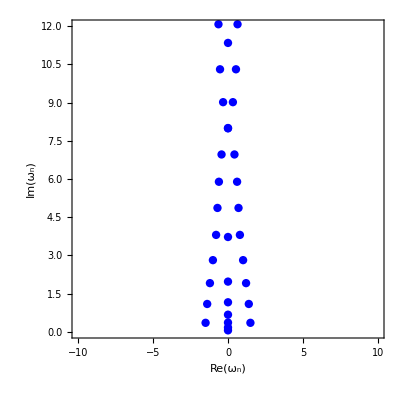

```mathematica
data2=Table[E2[[i]], {i,0,6*Nz+6}];
p4=ListPlot[{Re[#],Im[#]}&/@data2,AxesOrigin->{0,0},PlotRange->{{-10,10},{0,12}},ImagePadding->40,AspectRatio->1,Frame->True,
FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, 
PlotStyle->Directive[Blue,PointSize[.015]]
];
Show[p4]
```

# Graphics, figures...

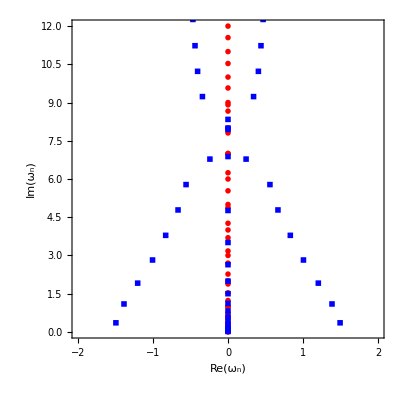

```mathematica
data1=Table[N[E1[[i]], Prec], {i,0,6*Nz+6}];
data2=Table[N[E2[[i]], Prec], {i,0,6*Nz+6}];

p3=ListPlot[{{Re[#],Im[#]}&/@data1, {Re[#],Im[#]}&/@data2},AxesOrigin->{0,0},PlotRange->{{-2,2},{0,12}},
ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None}, 
{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}},  RotateLabel->True, PlotMarkers->{{•,9},{■,2}} , 
PlotStyle->{Red,Blue}
];

Show[p3]
```

```mathematica
spaceh=Join[s1,sx, s2];
Length[spaceh]
```

```mathematica
spaceh=Join[s1,sx, s2];
Vtildy1= N[Table[(s1[[i]]^2)*(1-s1[[i]])*(6-3*s1[[i]])/4, {i,1,Nz+1 }] ,Prec  ];
Vtildx=N[Table[(sx[[i]]^2)*(1-sx[[i]])*(6-3*sx[[i]])/4, {i,1,Nz +1}] ,Prec  ];
Vtildy2=N[Table[(s2[[i]]^2)*(1-s2[[i]])*(6-3*s2[[i]])/4, {i,1,Nz +1}] ,Prec  ];
Vtild = Join[Vtildy1,  Vtildx,  Vtildy2];
Vt = ConstantArray[0,101];
V = Join[Vt,  Vtildx,  Vt];
```

```mathematica
rr=2/spaceh;
```

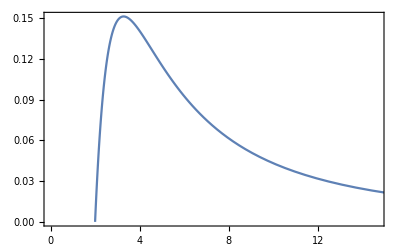

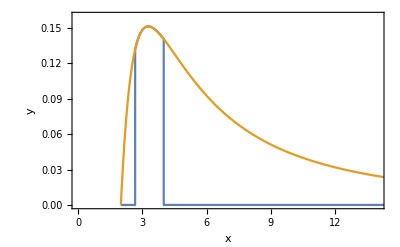
-Graphics-rPotential

```mathematica
ListLinePlot[Table[{rr[[k]],Vtild[[k]]},{k,1,303,1}],Frame->True,Axes->True]
Labeled[ListLinePlot[{Table[{rr[[k]],V[[k]]},{k,1,303,1}],Table[{rr[[k]],Vtild[[k]]},{k,1,303,1}]},Frame->True,Axes->True, AxesLabel->{"x","y"}, PlotRange->{{0,14},{0,0.16}}],{"r","Potential"},{Bottom,Left}]
```

```mathematica
data=Table[E1[[i]], {i,0,6*Nz+6}];
p1=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-2,2},{0,12}},ImagePadding->40,AspectRatio->1,Frame->True,
FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, 
PlotStyle->Directive[Red,PointSize[.015]]
];
```

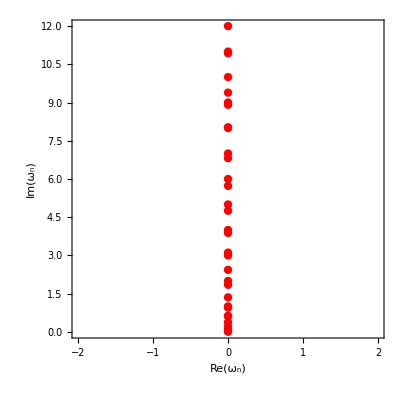

```mathematica
Show[p1]
```

```mathematica
p2=ListPlot[{Re[#],Im[#]}&/@data2,AxesOrigin->{0,0},PlotRange->{{-30,30},{0,12}},ImagePadding->40,AspectRatio->1,Frame->True,
FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, 
PlotStyle->Directive[Blue,PointSize[.015]]
];
```

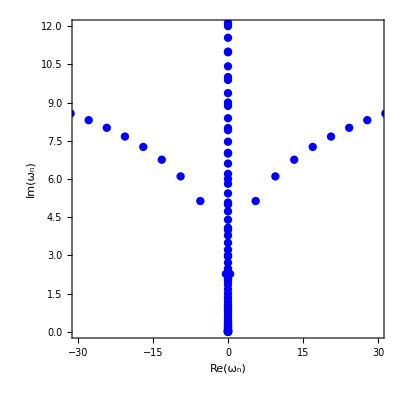

```mathematica
Show[p2]
```

```mathematica
R=Import["SW_full.dat"];
```

```mathematica
data=Table[R[[i]], {i,0,6*Nz+6}];
```

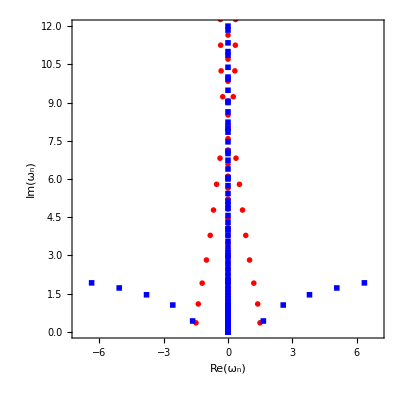

```mathematica
p3=ListPlot[{{Re[#],Im[#]}&/@data, {Re[#],Im[#]}&/@data2},AxesOrigin->{0,0},PlotRange->{{-7,7},{0,12}},
ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None}, 
{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}},  RotateLabel->True, PlotMarkers->{{•,9},{■,2}} , 
PlotStyle->{Red,Blue}
];

Show[p3]
```

```mathematica
Export["SW.dat",data,"Package"]
```

SW.dat

```mathematica
testd=Import["SW_cut.dat","Package"];
```

```mathematica
pp=ListPlot[{Re[#],Im[#]}&/@R,AxesOrigin->{0,0},PlotRange->{{-30,30},{0,12}},ImagePadding->40,AspectRatio->1,Frame->True,
FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, 
PlotStyle->Directive[Blue,PointSize[.015]]
];
```

```mathematica
Show[pp]
```

-Graphics-

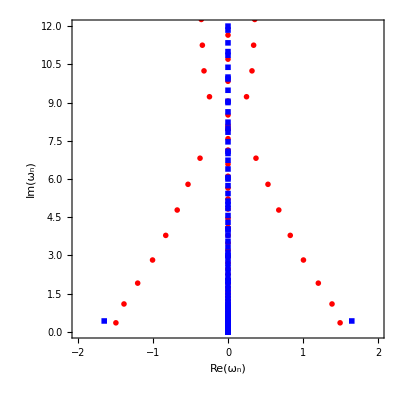

```mathematica
p3=ListPlot[{{Re[#],Im[#]}&/@data, {Re[#],Im[#]}&/@data2},AxesOrigin->{0,0},PlotRange->{{-2,2},{0,12}},
ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None}, 
{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}},  RotateLabel->True, PlotMarkers->{{•,9},{■,2}} , 
PlotStyle->{Red,Blue}];

Show[p3]
```